```mathematica
start=DateObject[];
```

```mathematica
RAW=Import["https://covid.ourworldindata.org/data/ecdc/full_data.csv"]
LATEST=RAW[[All,1]]//Rest//DeleteDuplicates//Sort//Last
```

{{date,location,new_cases,new_deaths,total_cases,total_deaths},{2019-12-31,Afghanistan,0,0,0,0},{2020-01-01,Afghanistan,0,0,0,0},{2020-01-02,Afghanistan,0,0,0,0},{2020-01-03,Afghanistan,0,0,0,0},{2020-01-04,Afghanistan,0,0,0,0},{2020-01-05,Afghanistan,0,0,0,0},{2020-01-06,Afghanistan,0,0,0,0},12491,{2020-04-15,Zimbabwe,0,0,17,3},{2020-04-16,Zimbabwe,6,0,23,3},{2020-04-17,Zimbabwe,1,0,24,3},{2020-04-18,Zimbabwe,0,0,24,3},{2020-04-19,Zimbabwe,1,0,25,3},{2020-04-20,Zimbabwe,0,0,25,3},{2020-04-21,Zimbabwe,0,0,25,3},{2020-04-22,Zimbabwe,3,0,28,3}}
 |  |  |  |

2020-04-22

```mathematica
COUNTRIES= {"Switzerland","Italy","South Korea","United Kingdom","United States","Japan","China","Germany","Sweden","France","India"};
ALLCOUNTRIES= (RAW//Rest)[[All,2]]//DeleteDuplicates;
ALLCOUNTRIES=Drop[ALLCOUNTRIES, Position[ALLCOUNTRIES,"World"]//Flatten];
```

```mathematica
(*Pop[country_]:=CountryData[
(*Print[country];*)
Interpreter["ComputedCountry"][country]
]["Population"]//First
If[!ValueQ[pops], pops =Association[#->Pop[#]&/@ALLCOUNTRIES]]*)
pops=<|"Afghanistan"->35530081,"Albania"->2930187,"Algeria"->41318142,"Andorra"->76965,"Angola"->29784193,"Anguilla"->14909,"Antigua and Barbuda"->102012,"Argentina"->44271041,"Armenia"->2930450,"Aruba"->105264,"Australia"->24450561,"Austria"->8735453,"Azerbaijan"->9827589,"Bahamas"->395361,"Bahrain"->1492584,"Bangladesh"->164669751,"Barbados"->285719,"Belarus"->9468338,"Belgium"->11429336,"Belize"->374681,"Benin"->11175692,"Bermuda"->61349,"Bhutan"->807610,"Bolivia"->11051600,"Bonaire Sint Eustatius and Saba"->21133,"Bosnia and Herzegovina"->3507017,"Botswana"->2291661,"Brazil"->209288278,"British Virgin Islands"->31196,"Brunei"->428697,"Bulgaria"->7084571,"Burkina Faso"->19193382,"Burundi"->10864245,"Cambodia"->16005373,"Cameroon"->24053727,"Canada"->36624199,"Cape Verde"->546388,"Cayman Islands"->61559,"Central African Republic"->4659080,"Chad"->14899994,"Chile"->18054726,"China"->1409517397,"Colombia"->49065615,"Congo"->81339988,"Costa Rica"->4905769,"Cote d'Ivoire"->24294750,"Croatia"->4189353,"Cuba"->11484636,"Curacao"->160539,"Cyprus"->1179551,"Czech Republic"->10618303,"Democratic Republic of Congo"->81339988,"Denmark"->5733551,"Djibouti"->956985,"Dominica"->73925,"Dominican Republic"->10766998,"Ecuador"->16624858,"Egypt"->97553151,"El Salvador"->6377853,"Equatorial Guinea"->1267689,"Eritrea"->5068831,"Estonia"->1309632,"Ethiopia"->104957438,"Faeroe Islands"->49290,"Falkland Islands"->2840,"Fiji"->905502,"Finland"->5523231,"France"->64979548,"French Polynesia"->686371,"Gabon"->2025137,"Gambia"->2100568,"Georgia"->3912061,"Germany"->82114224,"Ghana"->28833629,"Gibraltar"->34571,"Greece"->11159773,"Greenland"->56480,"Grenada"->107825,"Guam"->164229,"Guatemala"->16913503,"Guernsey"->65605,"Guinea"->12717176,"Guinea-Bissau"->1861283,"Guyana"->777859,"Haiti"->10981229,"Honduras"->9265067,"Hungary"->9721559,"Iceland"->335025,"India"->1339180127,"Indonesia"->263991379,"International"->"Population","Iran"->81162788,"Iraq"->38274618,"Ireland"->4761657,"Isle of Man"->84287,"Israel"->8321570,"Italy"->59359900,"Jamaica"->2890299,"Japan"->127484450,"Jersey"->95732,"Jordan"->9702353,"Kazakhstan"->18204499,"Kenya"->49699862,"Kosovo"->1859203,"Kuwait"->4136528,"Kyrgyzstan"->6045117,"Laos"->6858160,"Latvia"->1949670,"Lebanon"->6082357,"Liberia"->4731906,"Libya"->6374616,"Liechtenstein"->37922,"Lithuania"->2890297,"Luxembourg"->583455,"Macedonia"->2083159,"Madagascar"->25570895,"Malawi"->18622104,"Malaysia"->31624264,"Maldives"->436330,"Mali"->18541980,"Malta"->430835,"Mauritania"->4420184,"Mauritius"->1265138,"Mexico"->129163276,"Moldova"->4051212,"Monaco"->38695,"Mongolia"->3075647,"Montenegro"->628960,"Montserrat"->5177,"Morocco"->35739580,"Mozambique"->29668834,"Myanmar"->53370609,"Namibia"->2533794,"Nepal"->29304998,"Netherlands"->17035938,"New Caledonia"->276255,"New Zealand"->4705818,"Nicaragua"->6217581,"Niger"->21477348,"Nigeria"->190886311,"Northern Mariana Islands"->55144,"Norway"->5305383,"Oman"->4636262,"Pakistan"->197015955,"Palestine"->2731052,"Panama"->4098587,"Papua New Guinea"->8251162,"Paraguay"->6811297,"Peru"->32165485,"Philippines"->104918090,"Poland"->38170712,"Portugal"->10329506,"Puerto Rico"->3663131,"Qatar"->2639211,"Romania"->19679306,"Russia"->143989754,"Rwanda"->12208407,"Saint Helena"->4049,"Saint Kitts and Nevis"->55345,"Saint Lucia"->178844,"Saint Vincent and the Grenadines"->109897,"San Marino"->33400,"Sao Tome and Principe"->204327,"Saudi Arabia"->32938213,"Senegal"->15850567,"Serbia"->8790574,"Seychelles"->94737,"Sierra Leone"->7557212,"Singapore"->5708844,"Sint Maarten (Dutch part)"->"Population","Slovakia"->5447662,"Slovenia"->2079976,"Somalia"->14742523,"South Africa"->56717156,"South Korea"->50982212,"South Sudan"->12575714,"Spain"->46354321,"Sri Lanka"->20876917,"Sudan"->40533330,"Suriname"->563402,"Swaziland"->1367254,"Sweden"->9910701,"Switzerland"->8476005,"Syria"->18269868,"Taiwan"->23626456,"Tanzania"->57310019,"Thailand"->69037513,"Timor"->1296311,"Togo"->7797694,"Trinidad and Tobago"->1369125,"Tunisia"->11532127,"Turkey"->80745020,"Turks and Caicos Islands"->35446,"Uganda"->42862958,"Ukraine"->44222947,"United Arab Emirates"->9400145,"United Kingdom"->66181585,"United States"->324459463,"United States Virgin Islands"->104901,"Uruguay"->3456750,"Uzbekistan"->31910641,"Vatican"->792,"Venezuela"->31977065,"Vietnam"->95540800,"Yemen"->28250420,"Zambia"->17094130,"Zimbabwe"->16529903|>;
```

```mathematica
dat = RAW//Rest;
ts=<|"date"->1,"country"->2,"new_cases"->3,"new_deaths"->4,"total_cases"->5,"total_deaths"->6|>;
```

```mathematica
addSeries[what_,fun_]:=Module[{wrapper},
wrapper[row_]:=Function[{whattt}, row[[ts@whattt]]]; 
dat = Append[#, fun[wrapper[#]]]&/@dat;
ts[what]=Length[dat//First];
Print["++ series "<>what<>" @ "<>ToString[ts[what]]];
];
addSeries["date", DateObject[#["date"]]&]
addSeries["new_deaths_vs_new_cases", If[#["new_cases"]!=0,#["new_deaths"]/#["new_cases"],0]&]
addSeries["total_deaths_vs_total_cases", If[#["total_cases"]!=0,#["total_deaths"]/#["total_cases"],0]&]
addSeries["new_deaths_vs_pop",N[#["new_cases"] / pops[#["country"]]]&]
addSeries["total_deaths_vs_pop", N[#["total_deaths"] / pops[#["country"]]&]]
byCountry=GroupBy[dat,#[[ts@"country"]]&];
```

++ series date @ 22

++ series new_deaths_vs_new_cases @ 23

++ series total_deaths_vs_total_cases @ 24

++ series new_deaths_vs_pop @ 25

++ series total_deaths_vs_pop @ 26

```mathematica
ZipDate[ll_,idx_]:={#[[ts@"date"]],#[[idx]]}&/@ll;
PlotX[what_,who_,scale_]:=Module[ {},
DateListPlot[
Tooltip[
ZipDate[byCountry[#], ts@what]
,#]&/@who,
PlotRange->All,PlotLabels-> who,PlotLabel->what,ScalingFunctions->scale, ImageSize->Large, PlotTheme->"Detailed"
]
]
PlotXX[what_,who_]:=Grid[{{PlotX[what, who,None], PlotX[what,who,"Log"] }}]
```

```mathematica
PlotXX["total_deaths",COUNTRIES]
```

-Graphics-

```mathematica
PlotXX["new_deaths",COUNTRIES]
```

-Graphics-

```mathematica
PlotXX["total_cases",COUNTRIES].10
```

.10 -Graphics-

```mathematica
PlotXX["new_cases",COUNTRIES]
```

-Graphics-

```mathematica
PlotXX["new_deaths_vs_new_cases",COUNTRIES]
```

-Graphics-

```mathematica
PlotXX["total_deaths_vs_total_cases",COUNTRIES]
```

-Graphics-

```mathematica
PlotXX["new_deaths_vs_pop",COUNTRIES]
```

-Graphics-

```mathematica
PlotXX["new_deaths_vs_pop",{"Japan","South Korea","Switzerland","United Kingdom", "Sweden"}]
```

-Graphics-

```mathematica
PlotXX["new_deaths_vs_pop",{"Japan","India","Brazil","China","South Korea"}]
```

-Graphics-

```mathematica
PlotXX["new_deaths_vs_pop",{"Brazil","Russia", "Indonesia","India"}]
```

-Graphics-

```mathematica
PlotXX["new_deaths_vs_pop",{"Germany","France","Switzerland","Greece", "Spain","Norway","Denmark","Belgium"}]
```

-Graphics-

```mathematica
PlotXX["total_deaths_vs_pop",COUNTRIES]
```

-Graphics-

```mathematica
Delta[ts_]:=Drop[ts,1]-Drop[ts,-1]
Smooth[α_:.25]:=Function[ll,ExponentialMovingAverage[ll,α]]
RecentDeaths[cnt_,days_]:=byCountry[cnt][[-Range[days]//Reverse,ts@"new_deaths_vs_pop"]];
```

```mathematica
days=14;
α=1/3;
plot=ListPlot[Tooltip[Smooth[α]@RecentDeaths[#,days],#]&/@COUNTRIES,
PlotLabels->COUNTRIES,
PlotTheme->"Detailed", 
PlotRange->All,
PlotMarkers->None,
PlotLabel->"deaths / population",
ImagePadding->{{Automatic,180},{Automatic,Automatic}},
ImageSize->Full
]
(*Manipulate[plot,{{α,1},.01,1},{{days,7},3,100}]*)
```

-Graphics-

```mathematica
days=14;
α=.2;
plot=ListPlot[Tooltip[Smooth[α]@Delta@RecentDeaths[#,days],#]&/@COUNTRIES,
PlotLabels->COUNTRIES,
PlotTheme->"Detailed", 
PlotRange->All,
PlotMarkers->None,
PlotLabel->"∆ deaths / population",
ImagePadding->{{Automatic,180},{Automatic,Automatic}},
ImageSize->Full
]
(*Manipulate[plot,{{α,1/2},.01,1},{{days,7},3,100}]*)
```

-Graphics-

```mathematica
SelectNew[cnt_]:=Select[byCountry[cnt],#[[ts@"total_deaths"]]>0&]
FitX[ll_,deg_]:=Fit[ll,x^#&/@Range[0,deg],x]
```

```mathematica
ListLinePlot[
 SelectNew[#][[All,ts@"total_deaths_vs_pop"]]&/@COUNTRIES ,
ScalingFunctions->"Log",
PlotTheme->"Detailed", PlotLabels->COUNTRIES, PlotLabel->"Economists favorite chart"
]
```

-Graphics-

```mathematica
Forecast[cnts_]:=Module[{
curves=FitX[SelectNew[#][[All,ts["new_deaths_vs_pop"]]], 2]&/@cnts
},
Plot[
curves,
{x,0,50},
PlotLegends->None,
PlotTheme->"Detailed",
PlotLabel->"new_deaths/pop::forecast, as of day 1",
PlotLabels->cnts
] 
]
```

```mathematica
Forecast[COUNTRIES]
```

-Graphics-

```mathematica
Forecast[{"China","India","Japan","South Korea"}]
```

-Graphics-

```mathematica
GridX[rows_:-1]:=Function[dat, Grid[If[rows>-1,Take[dat, rows+1],dat], Frame->All,Alignment->Left]]
SortX[ll_,idx_]:=Sort[ll,#1[[idx]]>#2[[idx]]&]
TableXX[what_]:=Module[{mm,idx,vals,rank=0},
idx=ts@what; 
mm={
#,
Last[byCountry[#]][[idx]]//N, 
ListLinePlot[byCountry[#][[-Range[7]//Reverse,idx]],Axes->None,ImageSize->{15,15}]
}&/@ALLCOUNTRIES;
mm=Select[mm,NumericQ[#[[2]]]&];
mm=SortX[mm,2];
mm=Prepend[#,++rank]&/@mm;
mm = Prepend[mm,{"", "country", what, ""}];
mm
]
```

```mathematica
TableXX["total_deaths"]//GridX[20]
```

Part::partw: Part {-7,-6,-5,-4,-3,-2,-1} of {{2020-04-22,Saint Helena,3,0,3,0,DateObject[{2020,4,22},Day,Gregorian,1.],0,0,0.000740924,0}} does not exist.

Part::partw: Part {-7,-6,-5,-4,-3,-2,-1} of {{2020-04-22,Saint Helena,3.,0,3.,0,DateObject[{2020,4,22},Day,Gregorian,1.],0,0,0.000740924,0}} does not exist.

Part::partw: Part {-7,-6,-5,-4,-3,-2,-1} of {{2020-04-22,Saint Helena,3.,0.,3.,0.,DateObject[{2020,4,22},Day,Gregorian,1.],0.,0.,0.000740924,0.}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListLinePlot::lpn: {{2020-04-22,Saint Helena,3.,0.,3.,0.,DateObject[{2020,4,22},Day,Gregorian,1.],0.,0.,0.000740924,0.}}⟦{-7,-6,-5,-4,-3,-2,-1},6⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

| country | total_deaths | 
1 | United States | 45063. | -Graphics-
2 | Italy | 24648. | -Graphics-
3 | Spain | 21282. | -Graphics-
4 | France | 20796. | -Graphics-
5 | United Kingdom | 17337. | -Graphics-
6 | Iran | 6291. | -Graphics-
7 | Belgium | 5998. | -Graphics-
8 | Germany | 4879. | -Graphics-
9 | China | 4636. | -Graphics-
10 | Netherlands | 3916. | -Graphics-
11 | Brazil | 2741. | -Graphics-
12 | Turkey | 2259. | -Graphics-
13 | Canada | 1834. | -Graphics-
14 | Sweden | 1765. | -Graphics-
15 | Switzerland | 1186. | -Graphics-
16 | Mexico | 857. | -Graphics-
17 | Portugal | 762. | -Graphics-
18 | Ireland | 730. | -Graphics-
19 | India | 640. | -Graphics-
20 | Indonesia | 616. | -Graphics-

```mathematica
TableXX["new_deaths"]//GridX[20]
```

Part::partw: Part {-7,-6,-5,-4,-3,-2,-1} of {{2020-04-22,Saint Helena,3,0,3,0,DateObject[{2020,4,22},Day,Gregorian,1.],0,0,0.000740924,0}} does not exist.

Part::partw: Part {-7,-6,-5,-4,-3,-2,-1} of {{2020-04-22,Saint Helena,3.,0,3.,0,DateObject[{2020,4,22},Day,Gregorian,1.],0,0,0.000740924,0}} does not exist.

Part::partw: Part {-7,-6,-5,-4,-3,-2,-1} of {{2020-04-22,Saint Helena,3.,0.,3.,0.,DateObject[{2020,4,22},Day,Gregorian,1.],0.,0.,0.000740924,0.}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListLinePlot::lpn: {{2020-04-22,Saint Helena,3.,0.,3.,0.,DateObject[{2020,4,22},Day,Gregorian,1.],0.,0.,0.000740924,0.}}⟦{-7,-6,-5,-4,-3,-2,-1},4⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

| country | new_deaths | 
1 | United States | 2524. | -Graphics-
2 | Iran | 1082. | -Graphics-
3 | United Kingdom | 828. | -Graphics-
4 | Italy | 534. | -Graphics-
5 | France | 531. | -Graphics-
6 | Spain | 430. | -Graphics-
7 | Germany | 281. | -Graphics-
8 | Sweden | 185. | -Graphics-
9 | Belgium | 170. | -Graphics-
10 | Brazil | 166. | -Graphics-
11 | Netherlands | 165. | -Graphics-
12 | Mexico | 145. | -Graphics-
13 | Canada | 144. | -Graphics-
14 | Turkey | 119. | -Graphics-
15 | Russia | 51. | -Graphics-
16 | India | 50. | -Graphics-
17 | Switzerland | 45. | -Graphics-
18 | Ireland | 43. | -Graphics-
19 | Finland | 43. | -Graphics-
20 | Peru | 39. | -Graphics-

```mathematica
Append[#,1/(#[[3]])//IntegerPart]&/@TableXX@"total_deaths_vs_pop"//GridX[30]
```

Part::partw: Part {-7,-6,-5,-4,-3,-2,-1} of {{2020-04-22,Saint Helena,3,0,3,0,DateObject[{2020,4,22},Day,Gregorian,1.],0,0,0.000740924,0}} does not exist.

Part::partw: Part {-7,-6,-5,-4,-3,-2,-1} of {{2020-04-22,Saint Helena,3.,0,3.,0,DateObject[{2020,4,22},Day,Gregorian,1.],0,0,0.000740924,0}} does not exist.

Part::partw: Part {-7,-6,-5,-4,-3,-2,-1} of {{2020-04-22,Saint Helena,3.,0.,3.,0.,DateObject[{2020,4,22},Day,Gregorian,1.],0.,0.,0.000740924,0.}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListLinePlot::lpn: {{2020-04-22,Saint Helena,3.,0.,3.,0.,DateObject[{2020,4,22},Day,Gregorian,1.],0.,0.,0.000740924,0.}}⟦{-7,-6,-5,-4,-3,-2,-1},11⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

| country | total_deaths_vs_pop |  | IntegerPart[1/total_deaths_vs_pop]
1 | San Marino | 0.0011976 | -Graphics- | 835
2 | Belgium | 0.00052479 | -Graphics- | 1905
3 | Andorra | 0.000480738 | -Graphics- | 2080
4 | Spain | 0.000459116 | -Graphics- | 2178
5 | Italy | 0.00041523 | -Graphics- | 2408
6 | France | 0.000320039 | -Graphics- | 3124
7 | United Kingdom | 0.000261961 | -Graphics- | 3817
8 | Netherlands | 0.000229867 | -Graphics- | 4350
9 | Sweden | 0.00017809 | -Graphics- | 5615
10 | Ireland | 0.000153308 | -Graphics- | 6522
11 | Guernsey | 0.000152427 | -Graphics- | 6560
12 | Jersey | 0.000146242 | -Graphics- | 6838
13 | Switzerland | 0.000139924 | -Graphics- | 7146
14 | United States | 0.000138886 | -Graphics- | 7200
15 | Luxembourg | 0.000133686 | -Graphics- | 7480
16 | Isle of Man | 0.000118642 | -Graphics- | 8428
17 | Gibraltar | 0.000115704 | -Graphics- | 8642
18 | Bermuda | 0.0000815009 | -Graphics- | 12269
19 | Monaco | 0.0000775294 | -Graphics- | 12898
20 | Iran | 0.0000775109 | -Graphics- | 12901
21 | Portugal | 0.0000737693 | -Graphics- | 13555
22 | Denmark | 0.0000645324 | -Graphics- | 15496
23 | Germany | 0.0000594172 | -Graphics- | 16830
24 | Austria | 0.0000530024 | -Graphics- | 18867
25 | Canada | 0.0000500762 | -Graphics- | 19969
26 | Slovenia | 0.0000370197 | -Graphics- | 27012
27 | Northern Mariana Islands | 0.0000362687 | -Graphics- | 27571
28 | Panama | 0.0000344021 | -Graphics- | 29067
29 | Estonia | 0.0000328337 | -Graphics- | 30456
30 | British Virgin Islands | 0.0000320554 | -Graphics- | 31195

```mathematica
TableXX["new_deaths_vs_pop"]//GridX[]
```

Part::partw: Part {-7,-6,-5,-4,-3,-2,-1} of {{2020-04-22,Saint Helena,3,0,3,0,DateObject[{2020,4,22},Day,Gregorian,1.],0,0,0.000740924,0}} does not exist.

Part::partw: Part {-7,-6,-5,-4,-3,-2,-1} of {{2020-04-22,Saint Helena,3.,0,3.,0,DateObject[{2020,4,22},Day,Gregorian,1.],0,0,0.000740924,0}} does not exist.

Part::partw: Part {-7,-6,-5,-4,-3,-2,-1} of {{2020-04-22,Saint Helena,3.,0.,3.,0.,DateObject[{2020,4,22},Day,Gregorian,1.],0.,0.,0.000740924,0.}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListLinePlot::lpn: {{2020-04-22,Saint Helena,3.,0.,3.,0.,DateObject[{2020,4,22},Day,Gregorian,1.],0.,0.,0.000740924,0.}}⟦{-7,-6,-5,-4,-3,-2,-1},10⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

| country | new_deaths_vs_pop | 
1 | San Marino | 0.128862 | -Graphics-
2 | Saint Helena | 0.000740924 | ListLinePlot[{{2020-04-22,Saint Helena,3,0,3,0,Day: Wed 22 Apr 2020,0,0,0.000740924,0}}⟦{-7,-6,-5,-4,-3,-2,-1},10⟧,Axes→None,ImageSize→{15,15}]
3 | Singapore | 0.000444398 | -Graphics-
4 | Falkland Islands | 0.000352113 | -Graphics-
5 | Qatar | 0.000196271 | -Graphics-
6 | Bermuda | 0.000195602 | -Graphics-
7 | United States | 0.000114927 | -Graphics-
8 | Djibouti | 0.00010345 | -Graphics-
9 | Luxembourg | 0.000102836 | -Graphics-
10 | Spain | 0.0000856015 | -Graphics-
11 | Belgium | 0.0000851318 | -Graphics-
12 | Isle of Man | 0.0000830496 | -Graphics-
13 | Ireland | 0.0000814842 | -Graphics-
14 | United Kingdom | 0.0000649879 | -Graphics-
15 | Jersey | 0.000062675 | -Graphics-
16 | Turkey | 0.0000571057 | -Graphics-
17 | Sweden | 0.0000549911 | -Graphics-
18 | United Arab Emirates | 0.0000521269 | -Graphics-
19 | Portugal | 0.000049954 | -Graphics-
20 | Belarus | 0.0000484774 | -Graphics-
21 | Bonaire Sint Eustatius and Saba | 0.0000473194 | -Graphics-
22 | Peru | 0.0000470069 | -Graphics-
23 | Italy | 0.0000459738 | -Graphics-
24 | Bahrain | 0.0000442186 | -Graphics-
25 | Canada | 0.0000434139 | -Graphics-
26 | Netherlands | 0.0000427919 | -Graphics-
27 | France | 0.0000410437 | -Graphics-
28 | Panama | 0.0000397698 | -Graphics-
29 | Russia | 0.0000391833 | -Graphics-
30 | Maldives | 0.0000389613 | -Graphics-
31 | Saudi Arabia | 0.0000348228 | -Graphics-
32 | Denmark | 0.0000313942 | -Graphics-
33 | Serbia | 0.0000295771 | -Graphics-
34 | Malta | 0.0000278529 | -Graphics-
35 | Israel | 0.0000275188 | -Graphics-
36 | Germany | 0.0000272425 | -Graphics-
37 | Finland | 0.0000264338 | -Graphics-
38 | Armenia | 0.0000245696 | -Graphics-
39 | Kuwait | 0.0000205486 | -Graphics-
40 | Switzerland | 0.0000182869 | -Graphics-
41 | Chile | 0.0000180008 | -Graphics-
42 | Gabon | 0.0000177766 | -Graphics-
43 | Moldova | 0.0000162914 | -Graphics-
44 | Ecuador | 0.0000162407 | -Graphics-
45 | Iran | 0.0000159802 | -Graphics-
46 | Romania | 0.0000155493 | -Graphics-
47 | Iceland | 0.0000149243 | -Graphics-
48 | Greece | 0.0000139788 | -Graphics-
49 | Estonia | 0.0000129807 | -Graphics-
50 | Czech Republic | 0.0000119605 | -Graphics-
51 | Brazil | 0.0000119357 | -Graphics-
52 | Bosnia and Herzegovina | 0.0000114057 | -Graphics-
53 | Ukraine | 0.0000105601 | -Graphics-
54 | Cyprus | 0.0000101734 | -Graphics-
55 | Norway | 9.98985×10^-6 | -Graphics-
56 | Antigua and Barbuda | 9.80277×10^-6 | -Graphics-
57 | Albania | 8.53188×10^-6 | -Graphics-
58 | Dominican Republic | 7.43011×10^-6 | -Graphics-
59 | Hungary | 7.20049×10^-6 | -Graphics-
60 | Lithuania | 6.9197×10^-6 | -Graphics-
61 | Poland | 6.8901×10^-6 | -Graphics-
62 | Bulgaria | 6.49298×10^-6 | -Graphics-
63 | Croatia | 6.44491×10^-6 | -Graphics-
64 | Cameroon | 6.06975×10^-6 | -Graphics-
65 | Austria | 5.7238×10^-6 | -Graphics-
66 | Mexico | 5.64402×10^-6 | -Graphics-
67 | Guinea | 5.18983×10^-6 | -Graphics-
68 | Slovakia | 4.77269×10^-6 | -Graphics-
69 | Latvia | 4.61617×10^-6 | -Graphics-
70 | Morocco | 4.56077×10^-6 | -Graphics-
71 | Azerbaijan | 4.47719×10^-6 | -Graphics-
72 | Cuba | 4.35364×10^-6 | -Graphics-
73 | Kazakhstan | 4.17479×10^-6 | -Graphics-
74 | Kyrgyzstan | 3.6393×10^-6 | -Graphics-
75 | Colombia | 3.50551×10^-6 | -Graphics-
76 | Jamaica | 3.45985×10^-6 | -Graphics-
77 | Somalia | 3.32372×10^-6 | -Graphics-
78 | Kosovo | 3.22719×10^-6 | -Graphics-
79 | Uruguay | 3.18218×10^-6 | -Graphics-
80 | Japan | 2.96507×10^-6 | -Graphics-
81 | South Africa | 2.90917×10^-6 | -Graphics-
82 | Macedonia | 2.88024×10^-6 | -Graphics-
83 | Pakistan | 2.70536×10^-6 | -Graphics-
84 | Bangladesh | 2.63558×10^-6 | -Graphics-
85 | Argentina | 2.52987×10^-6 | -Graphics-
86 | Bahamas | 2.52933×10^-6 | -Graphics-
87 | Slovenia | 2.40387×10^-6 | -Graphics-
88 | Algeria | 2.25083×10^-6 | -Graphics-
89 | Senegal | 2.20812×10^-6 | -Graphics-
90 | Malaysia | 1.80241×10^-6 | -Graphics-
91 | Honduras | 1.72692×10^-6 | -Graphics-
92 | Afghanistan | 1.71686×10^-6 | -Graphics-
93 | Egypt | 1.60938×10^-6 | -Graphics-
94 | Montenegro | 1.58993×10^-6 | -Graphics-
95 | Georgia | 1.53372×10^-6 | -Graphics-
96 | Cote d'Ivoire | 1.52296×10^-6 | -Graphics-
97 | Tunisia | 1.47414×10^-6 | -Graphics-
98 | Tanzania | 1.46571×10^-6 | -Graphics-
99 | French Polynesia | 1.45694×10^-6 | -Graphics-
100 | Costa Rica | 1.42689×10^-6 | -Graphics-
101 | Indonesia | 1.4205×10^-6 | -Graphics-
102 | Philippines | 1.33437×10^-6 | -Graphics-
103 | Guatemala | 1.30074×10^-6 | -Graphics-
104 | Guyana | 1.28558×10^-6 | -Graphics-
105 | New Zealand | 1.27502×10^-6 | -Graphics-
106 | El Salvador | 1.09755×10^-6 | -Graphics-
107 | Uzbekistan | 1.09681×10^-6 | -Graphics-
108 | India | 1.03347×10^-6 | -Graphics-
109 | Bolivia | 9.95331×10^-7 | -Graphics-
110 | Burkina Faso | 9.89925×10^-7 | -Graphics-
111 | Sierra Leone | 9.26268×10^-7 | -Graphics-
112 | Venezuela | 9.069×10^-7 | -Graphics-
113 | Australia | 8.99775×10^-7 | -Graphics-
114 | Timor | 7.7142×10^-7 | -Graphics-
115 | Paraguay | 7.34075×10^-7 | -Graphics-
116 | Iraq | 7.31555×10^-7 | -Graphics-
117 | Trinidad and Tobago | 7.30393×10^-7 | -Graphics-
118 | Mali | 6.4718×10^-7 | -Graphics-
119 | Nigeria | 6.1293×10^-7 | -Graphics-
120 | Central African Republic | 4.29269×10^-7 | -Graphics-
121 | Liberia | 4.22663×10^-7 | -Graphics-
122 | Nepal | 3.75363×10^-7 | -Graphics-
123 | Sudan | 3.70066×10^-7 | -Graphics-
124 | Mongolia | 3.25135×10^-7 | -Graphics-
125 | Sri Lanka | 2.87399×10^-7 | -Graphics-
126 | Thailand | 2.75213×10^-7 | -Graphics-
127 | Togo | 2.56486×10^-7 | -Graphics-
128 | Rwanda | 2.45732×10^-7 | -Graphics-
129 | South Korea | 2.15762×10^-7 | -Graphics-
130 | Zimbabwe | 1.81489×10^-7 | -Graphics-
131 | Syria | 1.64205×10^-7 | -Graphics-
132 | Taiwan | 1.26976×10^-7 | -Graphics-
133 | Democratic Republic of Congo | 1.10647×10^-7 | -Graphics-
134 | Haiti | 9.10645×10^-8 | -Graphics-
135 | Chad | 6.71141×10^-8 | -Graphics-
136 | Congo | 6.14704×10^-8 | -Graphics-
137 | Malawi | 5.36996×10^-8 | -Graphics-
138 | Uganda | 4.66603×10^-8 | -Graphics-
139 | Myanmar | 3.74738×10^-8 | -Graphics-
140 | Ethiopia | 2.8583×10^-8 | -Graphics-
141 | China | 1.06419×10^-8 | -Graphics-
142 | Zambia | 0. | -Graphics-
143 | Yemen | 0. | -Graphics-
144 | Vietnam | 0. | -Graphics-
145 | Vatican | 0. | -Graphics-
146 | United States Virgin Islands | 0. | -Graphics-
147 | Turks and Caicos Islands | 0. | -Graphics-
148 | Swaziland | 0. | -Graphics-
149 | Suriname | 0. | -Graphics-
150 | South Sudan | 0. | -Graphics-
151 | Sint Maarten (Dutch part) | 0. | -Graphics-
152 | Seychelles | 0. | -Graphics-
153 | Sao Tome and Principe | 0. | -Graphics-
154 | Saint Vincent and the Grenadines | 0. | -Graphics-
155 | Saint Lucia | 0. | -Graphics-
156 | Saint Kitts and Nevis | 0. | -Graphics-
157 | Puerto Rico | 0. | -Graphics-
158 | Papua New Guinea | 0. | -Graphics-
159 | Palestine | 0. | -Graphics-
160 | Oman | 0. | -Graphics-
161 | Northern Mariana Islands | 0. | -Graphics-
162 | Niger | 0. | -Graphics-
163 | Nicaragua | 0. | -Graphics-
164 | New Caledonia | 0. | -Graphics-
165 | Namibia | 0. | -Graphics-
166 | Mozambique | 0. | -Graphics-
167 | Montserrat | 0. | -Graphics-
168 | Monaco | 0. | -Graphics-
169 | Mauritius | 0. | -Graphics-
170 | Mauritania | 0. | -Graphics-
171 | Madagascar | 0. | -Graphics-
172 | Liechtenstein | 0. | -Graphics-
173 | Libya | 0. | -Graphics-
174 | Lebanon | 0. | -Graphics-
175 | Laos | 0. | -Graphics-
176 | Kenya | 0. | -Graphics-
177 | Jordan | 0. | -Graphics-
178 | Guinea-Bissau | 0. | -Graphics-
179 | Guernsey | 0. | -Graphics-
180 | Guam | 0. | -Graphics-
181 | Grenada | 0. | -Graphics-
182 | Greenland | 0. | -Graphics-
183 | Gibraltar | 0. | -Graphics-
184 | Ghana | 0. | -Graphics-
185 | Gambia | 0. | -Graphics-
186 | Fiji | 0. | -Graphics-
187 | Faeroe Islands | 0. | -Graphics-
188 | Eritrea | 0. | -Graphics-
189 | Equatorial Guinea | 0. | -Graphics-
190 | Dominica | 0. | -Graphics-
191 | Curacao | 0. | -Graphics-
192 | Cayman Islands | 0. | -Graphics-
193 | Cape Verde | 0. | -Graphics-
194 | Cambodia | 0. | -Graphics-
195 | Burundi | 0. | -Graphics-
196 | Brunei | 0. | -Graphics-
197 | British Virgin Islands | 0. | -Graphics-
198 | Botswana | 0. | -Graphics-
199 | Bhutan | 0. | -Graphics-
200 | Benin | 0. | -Graphics-
201 | Belize | 0. | -Graphics-
202 | Barbados | 0. | -Graphics-
203 | Aruba | 0. | -Graphics-
204 | Anguilla | 0. | -Graphics-
205 | Angola | 0. | -Graphics-
206 | Andorra | 0. | -Graphics-

```mathematica
FmtX[d_,dp_]:=NumberForm[d, dp, ExponentFunction->(Null&),NumberSigns->{"-", "+"}];
MicroPlot[slope_]:=Plot[x slope,{x,0,1},PlotRange->{{0,1},{-.00001,.00001}},Axes->None,ImageSize->{15,15}];
(*MicroPlot[slope_]:=Graphics[Arrow[{{0,0},{1,slope}}],ImageSize->{20,20},Background->LightBlue]*)
DeathDelta[cnt_,offsets_]:=Module[{ idx=ts["new_deaths_vs_pop"] },
deltas=byCountry[cnt][[All,idx]]//Delta;
dd=deltas[[offsets]];
mm=AppendTo[dd,Mean[dd]];
mm=AppendTo[mm,StandardDeviation[dd]];
mm={cnt,{#,MicroPlot[#]}&/@mm};
mm//Flatten
]
DeathDeltas[cnts_,win_]:=Module[{},
offsets=-Range[win]//Reverse;
mm=DeathDelta[#,offsets]&/@cnts;
mm=Select[mm,NumberQ[#[[2 win+2]]]&];
mm=SortX[mm,2 win+2];
mm=Prepend[mm,{"",{"dT"<>ToString[#+1],""}&/@offsets,"Mean["<>ToString[win]<>"D]","", "σ"}//Flatten];
mm
]
```

```mathematica
DeathDeltas[COUNTRIES,7]//GridX[]
```

| dT-6 |  | dT-5 |  | dT-4 |  | dT-3 |  | dT-2 |  | dT-1 |  | dT0 |  | Mean[7D] |  | σ | 
United States | 9.94269×10^-6 | -Graphics- | 4.68163×10^-6 | -Graphics- | -2.57043×10^-6 | -Graphics- | 6.4384×10^-6 | -Graphics- | -0.0000256457 | -Graphics- | 0.0000106762 | -Graphics- | 0.0000284288 | -Graphics- | 4.56451×10^-6 | -Graphics- | 0.0000151322 | -Graphics-
Sweden | -1.51352×10^-6 | -Graphics- | 0.000013218 | -Graphics- | 6.35677×10^-6 | -Graphics- | -7.06307×10^-6 | -Graphics- | -4.33874×10^-6 | -Graphics- | -0.0000172541 | -Graphics- | 0.0000154379 | -Graphics- | 6.91893×10^-7 | -Graphics- | 0.0000108154 | -Graphics-
India | -9.93145×10^-8 | -Graphics- | 4.85372×10^-8 | -Graphics- | -1.19476×10^-8 | -Graphics- | 2.56127×10^-7 | -Graphics- | 1.63533×10^-7 | -Graphics- | -1.62786×10^-7 | -Graphics- | 3.65896×10^-8 | -Graphics- | 3.29626×10^-8 | -Graphics- | 1.33598×10^-7 | -Graphics-
China | 7.09463×10^-10 | -Graphics- | 2.14258×10^-7 | -Graphics- | -2.27738×10^-7 | -Graphics- | -9.22301×10^-9 | -Graphics- | -2.83785×10^-9 | -Graphics- | 1.27703×10^-8 | -Graphics- | -1.20609×10^-8 | -Graphics- | -3.44596×10^-9 | -Graphics- | 1.18376×10^-7 | -Graphics-
South Korea | -9.80734×10^-8 | -Graphics- | 0. | -Graphics- | -7.84587×10^-8 | -Graphics- | -1.96147×10^-7 | -Graphics- | 9.80734×10^-8 | -Graphics- | -7.84587×10^-8 | -Graphics- | 3.92294×10^-8 | -Graphics- | -4.48336×10^-8 | -Graphics- | 9.06252×10^-8 | -Graphics-
Japan | 2.11791×10^-7 | -Graphics- | 8.07942×10^-7 | -Graphics- | 3.37296×10^-7 | -Graphics- | -4.86334×10^-7 | -Graphics- | -1.38056×10^-6 | -Graphics- | -1.80414×10^-7 | -Graphics- | 8.6285×10^-8 | -Graphics- | -8.6285×10^-8 | -Graphics- | 6.48266×10^-7 | -Graphics-
Germany | 4.6277×10^-6 | -Graphics- | 6.25957×10^-6 | -Graphics- | 2.7888×10^-6 | -Graphics- | -0.0000140171 | -Graphics- | -8.31768×10^-6 | -Graphics- | 1.21782×10^-7 | -Graphics- | 5.50453×10^-6 | -Graphics- | -4.33194×10^-7 | -Graphics- | 7.20157×10^-6 | -Graphics-
Italy | -5.13815×10^-6 | -Graphics- | 0.0000188511 | -Graphics- | -4.93599×10^-6 | -Graphics- | -3.36928×10^-8 | -Graphics- | -7.4798×10^-6 | -Graphics- | -0.0000133255 | -Graphics- | 7.96834×10^-6 | -Graphics- | -5.8481×10^-7 | -Graphics- | 0.0000100053 | -Graphics-
Switzerland | 0.0000388155 | -Graphics- | -0.0000316187 | -Graphics- | 3.65738×10^-6 | -Graphics- | -2.47758×10^-6 | -Graphics- | 1.29778×10^-6 | -Graphics- | -0.0000198207 | -Graphics- | -1.53374×10^-6 | -Graphics- | -1.66858×10^-6 | -Graphics- | 0.0000203656 | -Graphics-
United Kingdom | -9.80635×10^-6 | -Graphics- | 2.11539×10^-7 | -Graphics- | 0.000014838 | -Graphics- | -1.11814×10^-6 | -Graphics- | 4.91073×10^-6 | -Graphics- | -0.0000177391 | -Graphics- | -5.66623×10^-6 | -Graphics- | -2.05279×10^-6 | -Graphics- | 9.70289×10^-6 | -Graphics-
France | -0.0000440754 | -Graphics- | 1.23116×10^-7 | -Graphics- | -0.0000344108 | -Graphics- | 0.0000333028 | -Graphics- | -0.0000274548 | -Graphics- | 0.0000194831 | -Graphics- | 9.47991×10^-6 | -Graphics- | -6.22174×10^-6 | -Graphics- | 0.0000272242 | -Graphics-

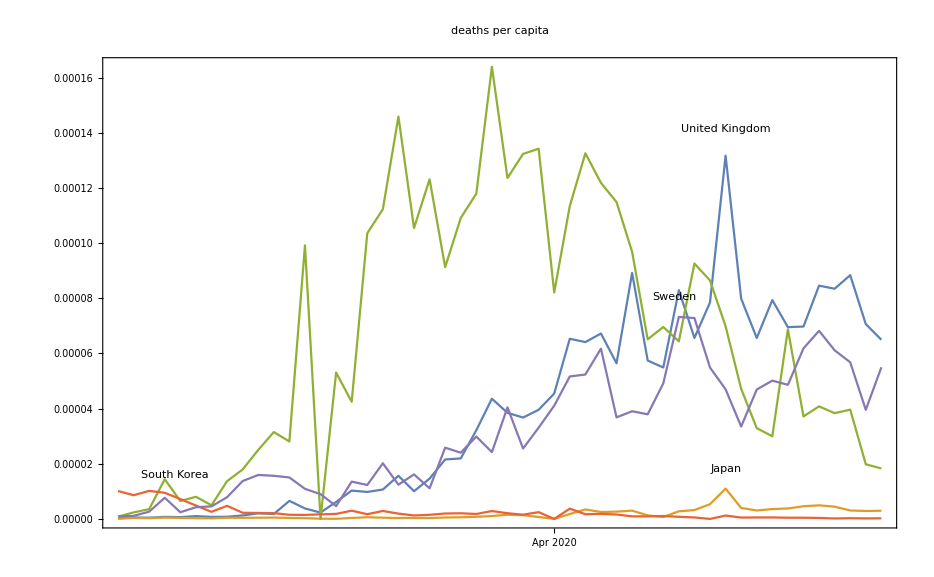

```mathematica
cnts={"United Kingdom","Japan","Switzerland","South Korea", "Sweden"};
DateListPlot[Tooltip[ZipDate[byCountry[#][[-Range[50]]],ts@"new_deaths_vs_pop"],#]&/@cnts,
PlotLabels->Placed[cnts,Above],PlotRange->All,PlotLabel->"deaths per capita"]
```

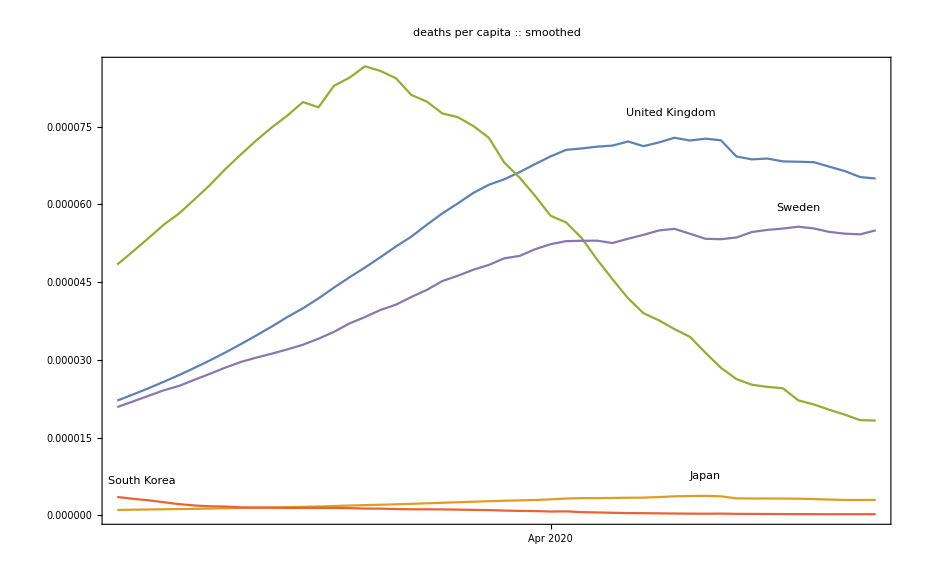

```mathematica
SmoothXX[α_]:=Function[{ll},
ret=ll;
ret[[All,2]]=ExponentialMovingAverage[ll[[All,2]],α];
ret
]
DateListPlot[Tooltip[SmoothXX[0.05]@ZipDate[byCountry[#][[-Range[50]]],ts@"new_deaths_vs_pop"],#]&/@cnts,
PlotLabels->Placed[cnts,Above],PlotRange->All,PlotLabel->"deaths per capita :: smoothed"]
```

```mathematica
(*DeathDeltas[ALLCOUNTRIES,7]//GridX[]*)
```

```mathematica
DateObject[]-start
DateObject[]
```

49.6105 s

Wed 22 Apr 2020 13:29:57GMT+1.